## Distribution plots of hedge performance

```mathematica
Clear["Global`*"]
```

```mathematica
days="90";
(*days="30";*)
```

### Customised plots

A customised Box-Whisker plot

```mathematica
ModifiedBoxWhiskerChart[d_,leg_,title_]:=Module[{s},
s=Quantile[#,{0.05,0.25, 0.5, 0.75, 0.95}]&/@Reverse[d];
BoxWhiskerChart[s, Method->{"BoxRange"->Identity},ChartLabels->Reverse[leg](*Placed[leg, Axis, Rotate[#,Pi/4]&]*), PlotTheme->"Classic", ChartStyle->Darker[Green], PlotLabel->title,PlotRange->{{-2,2},Automatic}, (*PlotRange->{{0.65,Length[leg]+0.35},{-2,2}},*)BarOrigin->Left]
]
```

The distribution chart (violin plot) has some unusual cropping in Mathematica; also, the scaling of the densities is misleading.

```mathematica
DistPlot[pos_, leg_,title_]:=Module[{d},
d=data[[pos]];
m1=Ceiling[Max[Abs[{Min[Quantile[#,0.05]&/@d], Max[Quantile[#, 0.95]&/@d]}]],0.1];
p4=DistributionChart[d,PlotTheme->"Classic",PlotRange->{-0.25,0.25},ChartLabels->{leg}, ChartStyle->Darker[Green],PlotLabel->title];
p4
]
```

### Load data

```mathematica
dataDirectory = "/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/";
prices =Import[dataDirectory <> "__prices.csv"];
```

```mathematica
nb=NotebookOpen[NotebookDirectory[] <> "boxplots_helper.nb"];
```

```mathematica
fn={
FileNames["PNL__KDE*BULLISH__4088__" <> days <> "*.csv", dataDirectory],
FileNames["PNL__KDE*CALM__8367__" <> days <> "*.csv", dataDirectory],
FileNames["PNL__KDE*COVID__9804__" <> days <> "*.csv", dataDirectory],
FileNames["PNL__SVCJ*BULLISH__4088__"<> days <> "*.csv", dataDirectory],
FileNames["PNL__SVCJ*CALM__8367__" <> days <> "*.csv", dataDirectory],
FileNames["PNL__SVCJ*COVID__9804__" <> days <> "*.csv", dataDirectory]
};

price={
Select[prices, StringContainsQ[#[[2]], "BULLISH__4088__"<> days]&][[1]][[-1]],
Select[prices, StringContainsQ[#[[2]], "CALM__8367__" <> days]&][[1]][[-1]],
Select[prices, StringContainsQ[#[[2]], "COVID__9804__" <> days]&][[1]][[-1]],
Select[prices, StringContainsQ[#[[2]], "BULLISH__4088__" <> days]&][[1]][[-1]],
Select[prices, StringContainsQ[#[[2]], "CALM__8367__" <> days]&][[1]][[-1]],
Select[prices, StringContainsQ[#[[2]], "COVID__9804__" <> days]&][[1]][[-1]]
};

fname={
"KDE_BULLISH_4088_" <> days,
"KDE_CALM_8367_" <> days,
"KDE_COVID_9804_" <> days,
"SVCJ_BULLISH_4088_" <> days,
"SVCJ_CALM_8367_" <> days,
"SVCJ_COVID_9804_" <> days
};
```

#### Call helper with each scenario

```mathematica
graphs={};
tables={};
For[kk=1, kk<=Length[fn], kk++,
data = Import[#]&/@fn[[kk]];
data=DeleteCases[Flatten[data[[#]]],_?StringQ]&/@Range[Length[data]];
data = data /price[[kk]];
legend=StringSplit[StringSplit[#,"/"][[-1]], "__"][[2;;-3]]&/@fn[[kk]];
legend=StringReplace[#, {"BLACK_SCHOLES"-> "BS", "HESTON" -> "Heston", "MERTON"->"Merton", "VARIANCE_GAMMA"->"VG", "DeltaHedge"->"Delta", "DeltaGammaHedge"->"D.-Gamma", "DeltaVegaHedge"->"D.-Vega", "MinimumVarianceHedge"->"MV"}]&/@legend;
NotebookEvaluate[nb];
AppendTo[graphs, plot];
AppendTo[tables, t3];
];
```

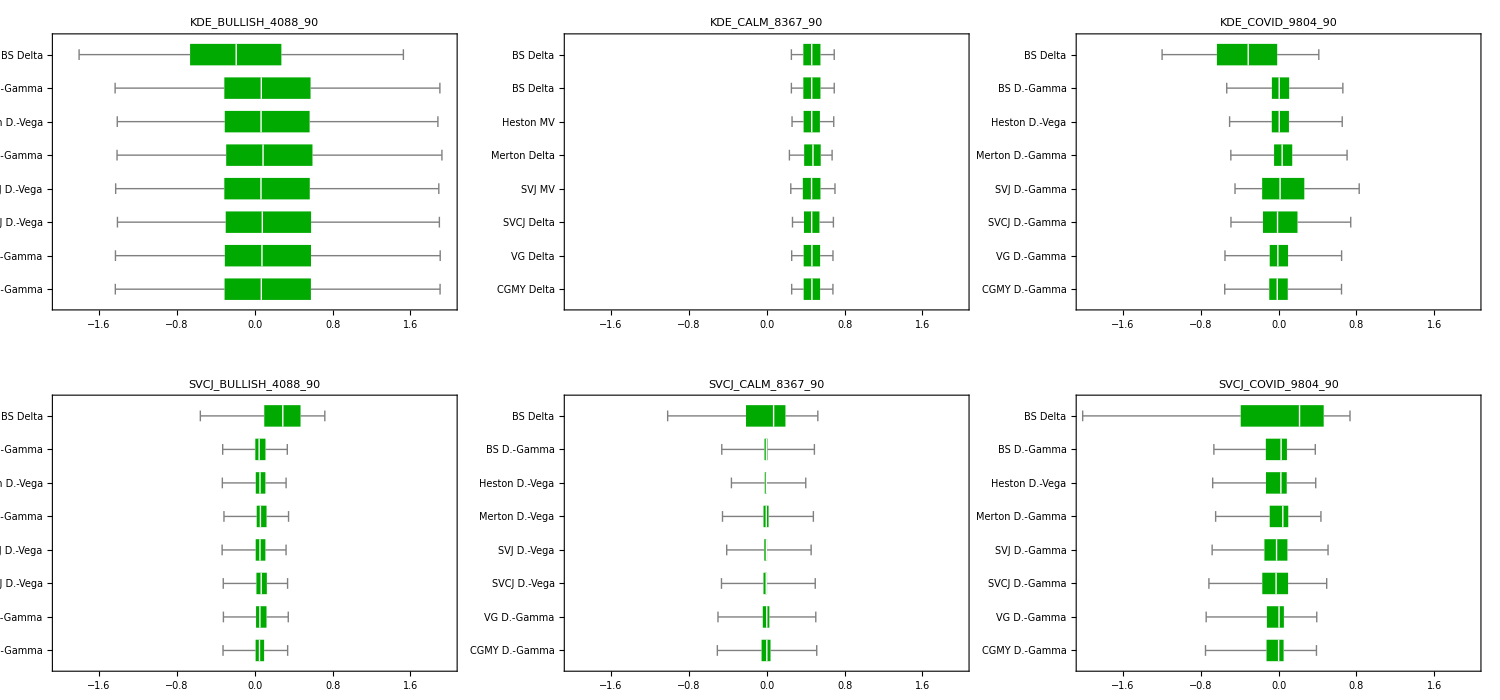

```mathematica
GraphicsGrid[{graphs[[1;;3]], graphs[[4;;6]]}, ImageSize->{1500,700}]
```

```mathematica
Export[NotebookDirectory[] <> "graphs_" <> days <> "d_all.pdf", %]
```

/Users/nat/Documents/GitHub/hedging_cc/_mathematica/graphs_90d_all.pdf

```mathematica
Table[Export[NotebookDirectory[] <> "graphs_" <> days <>"d_" <> ToString[k] <> ".pdf", graphs[[k]]], {k,1,Length[graphs]}];
```

```mathematica
{tables[[1;;3]], tables[[4;;]]}//TableForm
```

| BS Delta | BS D.-Gamma | Heston D.-Vega | Merton D.-Gamma | SVJ D.-Vega | SVCJ D.-Vega | VG D.-Gamma | CGMY D.-Gamma
Min | -6.55 | -6.36 | -6.35 | -6.32 | -6.35 | -6.34 | -6.36 | -6.37
5% ES | -2.38 | -1.99 | -1.95 | -1.96 | -1.97 | -1.95 | -1.98 | -1.99
95% ES | 2.43 | 2.83 | 2.8 | 2.85 | 2.81 | 2.81 | 2.83 | 2.83
Max | 11.46 | 11.73 | 11.74 | 11.76 | 11. | 11.73 | 11.72 | 11.71
Hedge error | 101.91 | 101.76 | 100.3 | 101.77 | 101.02 | 100.72 | 101.75 | 101.75 |  | BS Delta | BS Delta | Heston MV | Merton Delta | SVJ MV | SVCJ Delta | VG Delta | CGMY Delta
Min | -0.29 | -0.29 | -0.27 | -0.28 | -0.25 | -0.25 | -0.28 | -0.28
5% ES | 0.18 | 0.18 | 0.2 | 0.15 | 0.19 | 0.2 | 0.19 | 0.19
95% ES | 0.76 | 0.76 | 0.76 | 0.73 | 0.77 | 0.75 | 0.75 | 0.75
Max | 1.04 | 1.04 | 1.06 | 1.05 | 1.12 | 1.07 | 1.12 | 1.12
Hedge error | 13.59 | 13.59 | 13.11 | 13.53 | 13.82 | 12.82 | 13.18 | 13.18 |  | BS Delta | BS D.-Gamma | Heston D.-Vega | Merton D.-Gamma | SVJ D.-Gamma | SVCJ D.-Gamma | VG D.-Gamma | CGMY D.-Gamma
Min | -4.36 | -2.69 | -2.64 | -2.64 | -2.44 | -2.58 | -2.7 | -2.71
5% ES | -1.56 | -0.8 | -0.76 | -0.77 | -0.7 | -0.78 | -0.83 | -0.84
95% ES | 0.6 | 0.93 | 0.9 | 0.97 | 1.11 | 1. | 0.91 | 0.9
Max | 3.88 | 3.33 | 3.32 | 4.52 | 4.57 | 4.45 | 4.49 | 4.55
Hedge error | 50.06 | 34.48 | 33.09 | 34.57 | 40.02 | 37.4 | 34.63 | 34.67
 | BS Delta | BS D.-Gamma | Heston D.-Vega | Merton D.-Gamma | SVJ D.-Vega | SVCJ D.-Vega | VG D.-Gamma | CGMY D.-Gamma
Min | -14.67 | -11.58 | -11.57 | -11.51 | -11.55 | -9.3 | -11.6 | -11.6
5% ES | -1.1 | -0.64 | -0.63 | -0.62 | -0.63 | -0.62 | -0.63 | -0.63
95% ES | 0.84 | 0.64 | 0.62 | 0.66 | 0.62 | 0.64 | 0.65 | 0.65
Max | 10.14 | 11.42 | 11.29 | 11.34 | 11.26 | 9.02 | 11.27 | 11.27
Hedge error | 44.14 | 26.5 | 25.86 | 26.45 | 25.89 | 25.26 | 26.55 | 26.39 |  | BS Delta | BS D.-Gamma | Heston D.-Vega | Merton D.-Vega | SVJ D.-Vega | SVCJ D.-Vega | VG D.-Gamma | CGMY D.-Gamma
Min | -12.63 | -8.68 | -12.75 | -6.32 | -7.79 | -12.75 | -12.73 | -12.74
5% ES | -1.56 | -0.85 | -0.71 | -0.79 | -0.78 | -0.89 | -0.96 | -0.97
95% ES | 0.88 | 0.82 | 0.69 | 0.77 | 0.79 | 0.88 | 0.89 | 0.9
Max | 7.74 | 5.19 | 7.79 | 4.15 | 7.78 | 8.99 | 8.97 | 9.25
Hedge error | 53.39 | 33.36 | 28.28 | 31.01 | 31.26 | 36.05 | 38.82 | 39.09 |  | BS Delta | BS D.-Gamma | Heston D.-Vega | Merton D.-Gamma | SVJ D.-Gamma | SVCJ D.-Gamma | VG D.-Gamma | CGMY D.-Gamma
Min | -13.53 | -7.89 | -7.9 | -14.3 | -11.76 | -11.75 | -20.99 | -11.72
5% ES | -2.77 | -1.18 | -1.26 | -1.34 | -1.36 | -1.39 | -1.26 | -1.25
95% ES | 0.87 | 0.71 | 0.68 | 0.78 | 0.94 | 0.93 | 0.73 | 0.73
Max | 13.48 | 10.78 | 10.77 | 13.6 | 13.66 | 13.6 | 13.67 | 13.65
Hedge error | 88.42 | 38.24 | 39.34 | 43.95 | 48. | 49.06 | 42.99 | 41.27

```mathematica
Export[NotebookDirectory[] <> "tables_"<> days <>"d_all.pdf", {tables[[1;;3]],{},{}, tables[[4;;]]}//TableForm]
```

/Users/nat/Documents/GitHub/hedging_cc/_mathematica/tables_90d_all.pdf

```mathematica
Export[NotebookDirectory[] <> "tables_" <> days <> "d_all.tex", {tables[[1;;3]], tables[[4;;]]}//TableForm]
```

/Users/nat/Documents/GitHub/hedging_cc/_mathematica/tables_90d_all.tex

```mathematica
models
```

{*BLACK*,*HESTON*,*MERTON*,*SVJ*,*__*__*SVCJ*,*VARIANCE_GAMMA*,*CGMY*}

```mathematica
legend=StringReplace[#, {"BLACK_SCHOLES"-> "BS", "HESTON" -> "Heston", "MERTON"->"Merton", "VARIANCE_GAMMA"->"VG", "Delta"->"D", "D.-Gamma"->"DG", "D.-Vega"->"DV"}]&/@legend;
```

```mathematica
Flatten[Position[legend[[;;,3]], "D"]]
```

{2,5,7,11,15,19,23}

```mathematica
dpos = Flatten[Position[legend[[;;,3]], "D"]];
dgpos = Flatten[Position[legend[[;;,3]], "DG"]];
dvpos = Flatten[Position[legend[[;;,3]], "DV"]];
mvpos = Flatten[Position[legend[[;;,3]], "MV"]];
```

```mathematica
legend[[dpos]]
```

(SVCJ | BS | D | COVID | 9804
SVCJ | CGMY | D | COVID | 9804
SVCJ | Heston | D | COVID | 9804
SVCJ | Merton | D | COVID | 9804
SVCJ | SVCJ | D | COVID | 9804
SVCJ | SVJ | D | COVID | 9804
SVCJ | VG | D | COVID | 9804)

```mathematica
legend[[dgpos]]
```

(SVCJ | BS | DG | COVID | 9804
SVCJ | CGMY | DG | COVID | 9804
SVCJ | Heston | DG | COVID | 9804
SVCJ | Merton | DG | COVID | 9804
SVCJ | SVCJ | DG | COVID | 9804
SVCJ | SVJ | DG | COVID | 9804
SVCJ | VG | DG | COVID | 9804)

```mathematica
legend[[dvpos]]
```

(SVCJ | BS | DV | COVID | 9804
SVCJ | Heston | DV | COVID | 9804
SVCJ | Merton | DV | COVID | 9804
SVCJ | SVCJ | DV | COVID | 9804
SVCJ | SVJ | DV | COVID | 9804)

```mathematica
legend[[mvpos]]
```

(SVCJ | Heston | MV | COVID | 9804
SVCJ | Merton | MV | COVID | 9804
SVCJ | SVCJ | MV | COVID | 9804
SVCJ | SVJ | MV | COVID | 9804)

```mathematica
models
```

{*BLACK*,*HESTON*,*MERTON*,*SVJ*,*__*__*SVCJ*,*VARIANCE_GAMMA*,*CGMY*}

```mathematica
models2={"BS", "Heston", "Merton", "SVJ", "SVCJ", "CGMY"};
```

```mathematica
pos2=Table[Flatten[Position[legend[[;;,2]], models2[[jj]]]], {jj, 1,Length[models2]}]
```

{{1,2,3},{6,7,8,9},{10,11,12,13},{18,19,20,21},{14,15,16,17},{4,5}}

```mathematica
leghedge={"Delta", "Delta-Gamma", "Delta-Vega", "MV"};
```

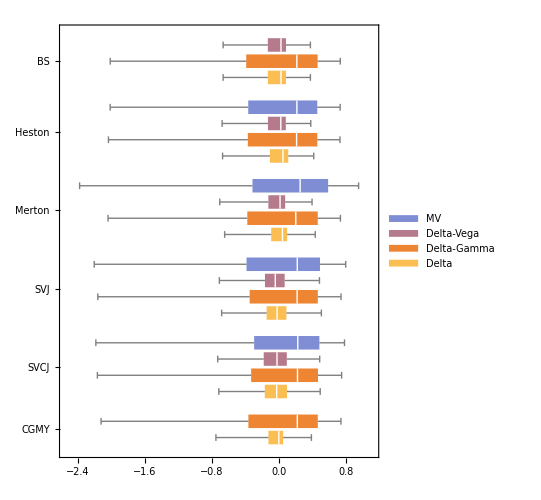

```mathematica
s=Quantile[#,{0.05,0.25, 0.5, 0.75, 0.95}]&/@d;
BoxWhiskerChart[s[[#]]&/@Reverse[pos2], Method->{"BoxRange"->Identity},(*ChartLabels->Placed[Range[1,21], Axis, Rotate[#,Pi/4]&],*)ChartLabels->{Placed[Reverse[models2],Axis],None},(* LabelingFunction->(Placed[#2.{3,1}-3,After]&),*)PlotLabel->"",(*PlotRange->{{0.65,Length[legend]+0.35},{-2.5,1}},*)BarOrigin->Left,ChartLegends->leghedge,AspectRatio->1.25,BarSpacing->{0.2,1}]
```

```mathematica
graphs={};
For[kk=1, kk<=Length[fn], kk++,
data = Import[#]&/@fn[[kk]];
data=DeleteCases[Flatten[data[[#]]],_?StringQ]&/@Range[Length[data]];
data = data /price[[kk]];
s=Quantile[#,{0.05,0.25, 0.5, 0.75, 0.95}]&/@data;
g=BoxWhiskerChart[s[[#]]&/@Reverse[pos2], Method->{"BoxRange"->Identity},(*ChartLabels->Placed[Range[1,21], Axis, Rotate[#,Pi/4]&],*)ChartLabels->{Placed[Reverse[models2],Axis],None},(* LabelingFunction->(Placed[#2.{3,1}-3,After]&),*)PlotLabel->fname[[kk]],PlotRange->{{-2,2}, Automatic},(*PlotRange->{{0.65,Length[legend]+0.35},{-2.5,1}},*)BarOrigin->Left,ChartLegends->leghedge,AspectRatio->1.25,BarSpacing->{0.2,1}];
AppendTo[graphs,g];
Export[NotebookDirectory[] <> fname[[kk]] <> "_full_graph.pdf", g]
]
```

```mathematica
Table[Export[NotebookDirectory[] <> "graphs_"<> days <> "d_full_" <> ToString[k] <> ".pdf", graphs[[k]]], {k,1,Length[graphs]}];
```